```mathematica
ClearAll["Global`*"]
$PlotTheme = "Monochrome";
```

# Rectangle -- eigenvalues and eigenvectors

Tady v import je potřeba si zadat správnou cestu k obrázku.

```mathematica
RectangleShapePicture=Import["C:\\Users\\matya\\Desktop\\MatFyz\\Počítačové řešení fyzikálních úloh\\Polynomiální aproximace\\rectangle2.png"] (* first we get an image of guitar shape *)
```

-Graphics-

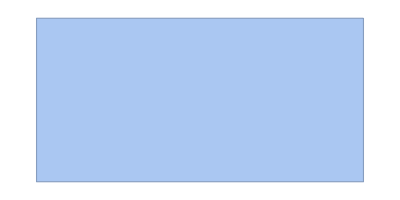

```mathematica
RectangleShapeMesh= ImageMesh[RectangleShapePicture] (* create mesh out of a black-and-white figure *)
```

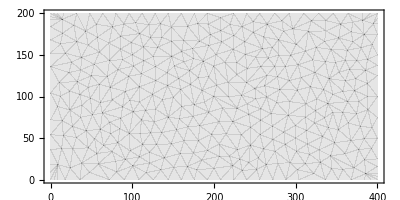

```mathematica
ContourPlot[256,  {x, y} ∈ RectangleShapeMesh,AspectRatio->Automatic]
```

```mathematica
{RectangleEigenvalues,RectangleEigenvectors}=NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈RectangleShapeMesh,6]; (* Solve eigenvalue problem for the Laplace operator with Dirichlet boundary condition. *)
```

```mathematica
RectangleEigenvalues = RectangleEigenvalues*10000
```

{3.08428,4.93493,8.01956,10.4877,12.3389,12.339}

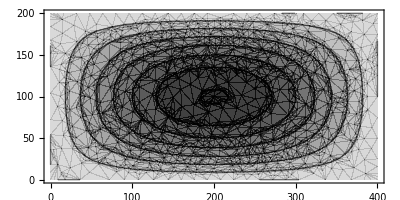
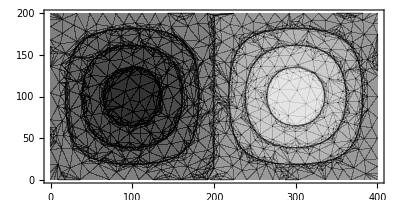
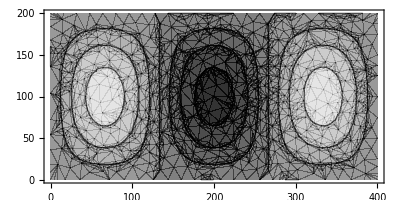
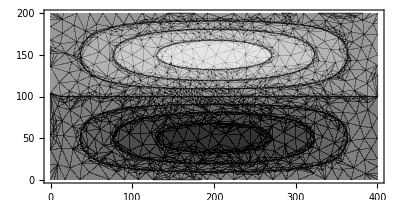
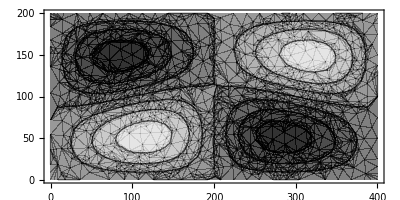
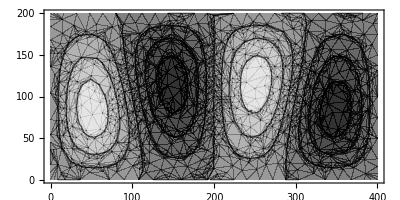

```mathematica
ContourPlot[#, {x, y} ∈ RectangleShapeMesh,AspectRatio->Automatic] & /@ RectangleEigenvectors (* Rough plot of eigenfunctions. *)
```

```mathematica
{RectangleEigenvaluesFine,RectangleEigenvectorsFine}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},
u[x,y],
{x,y}∈RectangleShapeMesh,
6, 
Method->{"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.3}}}}
]; (* Some fine tuning. Play with MaxCellMeasure in order to get better (more accurate) results. *)
```

```mathematica
RectangleEigenvaluesFine = RectangleEigenvaluesFine*10000(* Show the eigenvalues. *)
```

{3.08425,4.9348,8.01905,10.4865,12.337,12.337}

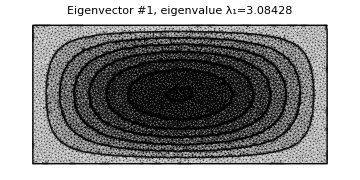
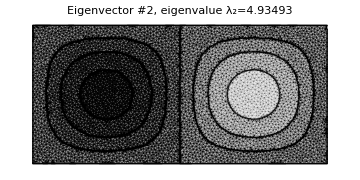
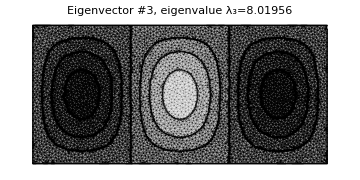
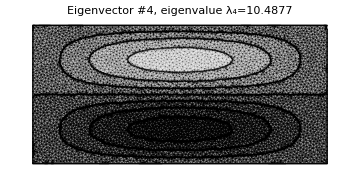
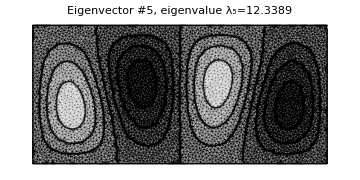
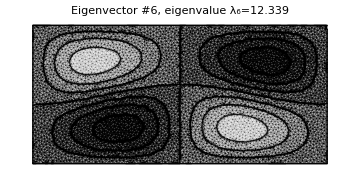

```mathematica
Table[
ContourPlot[
RectangleEigenvectorsFine⟦n⟧,
{x,y}∈RectangleShapeMesh,
Frame->None,
BoundaryStyle->{Thick,Black},
PlotLabel->StringTemplate["Eigenvector #``, eigenvalue λ_(``)=``"][n, n, RectangleEigenvalues[[n]]], 
ImageSize->Medium, 
PlotPoints->50,
AspectRatio->Automatic
],
{n,1,6}
] (* We are ready to visualise the eigenvalues and the corresponding eigenvectors *)
```

```mathematica
Directory[]
```

C:\Users\matya\Documents

```mathematica
(* Export the plots. *)
Table[
Export[
StringTemplate["rectangle-eigenvector-``.png"][n],
ContourPlot[
RectangleEigenvectorsFine⟦n⟧,
{x,y}∈RectangleShapeMesh,
Frame->None,
BoundaryStyle->{Thick,Black},
PlotLabel->StringTemplate["Eigenvector #``, eigenvalue λ_(``)=``"][n, n, RectangleEigenvalues[[n]]], 
ImageSize->Medium, 
PlotPoints->50,
AspectRatio->Automatic
]
],
{n,1,6}
] (* We are ready to visualise the eigenvalues and the corresponding eigenvectors *)
```

{rectangle-eigenvector-1.png,rectangle-eigenvector-2.png,rectangle-eigenvector-3.png,rectangle-eigenvector-4.png,rectangle-eigenvector-5.png,rectangle-eigenvector-6.png}